#### Synopsis

This notebook:
 - calculates the modular flow of a generic boosted interval in Poincaré AdS_3,
 - from first principle, starting from the basic isometries;
 - it matches Luis’s results and further confirms them for a generic boosted interval.

#### Setup

```mathematica
SetDirectory@NotebookDirectory[];
<<"Physica/MathUtils.wl"
```

/home/bryan/Documents/Base/Github/journal/nb/modFlowPoincare.nb

```mathematica
<<Notation`
Symbolize[Subscript[_, _]];
```

```mathematica
dX[n_]:=Symbol["d"<>ToString[coord[[n]]]]
```

```mathematica
$Assumptions=And[u∈Reals,z∈Reals,v∈Reals,z≥0];
```

```mathematica
coord={u,v,z};
dim=Length[coord];
metricSign=-1;
```

```mathematica
ds2=(+du dv+dz^2)/z^2;
```

```mathematica
metric=Table[1/2 D[ds2,dX[i],dX[j]],{i,1,dim},{j,1,dim}]
```

{{0,1/(2 z^2),0},{1/(2 z^2),0,0},{0,0,1/z^2}}

```mathematica
(*<<"diffgeoM.wl"*)
<<diffgeoM`
```

```mathematica
Einstein- metric
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[#2,#1]))/.Directive[x_,__]:>x&[Plot,"Web"]
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

#### Killing vectors

Usual bulk Killings:

Translation:

```mathematica
pu={1,0,0};
pv={0,1,0};
```

```mathematica
lieD[#,g]&/@{pu,pv}
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

Rotation (boost):

```mathematica
muv={u,-v,0};
```

```mathematica
lieD[muv,g]
```

{{0,0,0},{0,0,0},{0,0,0}}

Note: rotation / boost is very similar to scaling in lightcone coordinates.

Scaling:

```mathematica
Δ={u,v,z};
```

```mathematica
lieD[Δ,g]
```

{{0,0,0},{0,0,0},{0,0,0}}

Special conformal:

```mathematica
ku={z^2+u*v,0,0}-v Δ
kv={0,z^2+u*v,0}-u Δ
```

{z^2,-v^2,-v z}

{-u^2,z^2,-u z}

```mathematica
lieD[#,g]&/@{ku,kv}
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

Combine bulk Killings to match the expected ones at the boundary:

```mathematica
bulkKillings=Function[
{u,v,z,apu,apv,a0,auv,aku,akv},
pu apu+ pv apv+Δ a0+muv auv+ku aku+kv akv//Evaluate
];

bulkToBoundaryKillings=Function[
{u,v,apu,apv,a0,auv,aku,akv},
(bulkKillings[u,v,0,apu,apv,a0,auv,aku,akv]//Collect[#,{u,v}]&)⟦;;-2⟧//Evaluate
];
```

Get coefficients for j_u

```mathematica
(-u^(#+1){1,0})&/@Range[-1,1]
{
#==bulkToBoundaryKillings[u,v,apu,apv,a0,auv,aku,akv]
}&/@%
bulkKillings⟦1⟧
```

{{-1,0},{-u,0},{-u^2,0}}

{{{-1,0}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}},{{-u,0}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}},{{-u^2,0}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}}}

{u,v,z,apu,apv,a0,auv,aku,akv}

```mathematica
ju=Function[{n},Piecewise[{{bulkKillings[u,v,z,-1,0,0,0,0,0], n==-1}, {bulkKillings[u,v,z,0,0,-1/2,-1/2,0,0], n==0}, {bulkKillings[u,v,z,0,0,0,0,0,1], n==1}}]//Evaluate]
```

Function[{n},Piecewise[{{{-1,0,0}, n==-1}, {{-u,0,-z/2}, n==0}, {{-u^2,z^2,-u z}, n==1}, {0, True}}]]

Get coefficients for j_v

```mathematica
(-v^(#+1){0,1})&/@Range[-1,1]
{
#==bulkToBoundaryKillings[u,v,apu,apv,a0,auv,aku,akv]
}&/@%
bulkKillings⟦1⟧
```

{{0,-1},{0,-v},{0,-v^2}}

{{{0,-1}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}},{{0,-v}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}},{{0,-v^2}=={apu+(a0+auv) u-akv u^2,apv+(a0-auv) v-aku v^2}}}

{u,v,z,apu,apv,a0,auv,aku,akv}

```mathematica
jv=Function[{n},Piecewise[{{bulkKillings[u,v,z,0,-1,0,0,0,0], n==-1}, {bulkKillings[u,v,z,0,0,-1/2,1/2,0,0], n==0}, {bulkKillings[u,v,z,0,0,0,0,1,0], n==1}}]//Evaluate]
```

Function[{n},Piecewise[{{{0,-1,0}, n==-1}, {{0,-v,-z/2}, n==0}, {{z^2,-v^2,-v z}, n==1}, {0, True}}]]

Check Killing’s equation:

```mathematica
lieD[ju[#1],metric]&/@Range[-1,1]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
lieD[jv[#1],metric]&/@Range[-1,1]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

Check the algebra: [L_m,L_n]=(m-n)L_(m+n)

```mathematica
Subsets[{-1,0,1},{2}]
```

{{-1,0},{-1,1},{0,1}}

```mathematica
(
lieD[ju[#1],ju[#2],{up}]
-(#1-#2)ju[#1+#2]
)&@@@Subsets[{-1,0,1},{2}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(
lieD[jv[#1],jv[#2],{up}]
-(#1-#2)jv[#1+#2]
)&@@@Subsets[{-1,0,1},{2}]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
lieD[ju[#1],jv[#2],{up}]&@@@Tuples[{-1,0,1},2]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

#### Derivation of bulk mod flow

```mathematica
coeffNames={lm,l0,lp,Lm,L0,Lp};

χdef=HoldForm[2π(
{lm,l0,lp}.(ju/@Range[-1,1])
-{Lm,L0,Lp}.(jv/@Range[-1,1])
)];

χ=FullSimplify[ReleaseHold[χdef]]
```

{-2 π (lm+u (l0+lp u)+Lp z^2),2 π (Lm+v (L0+Lp v)+lp z^2),π (-l0+L0-2 lp u+2 Lp v) z}

```mathematica
lieD[χ,metric]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
uv2xt={u->x+t,v->x-t};
xt2uv=Solve[uv2xt/.Rule->Equal,{x,t}]//First
```

{x→(u+v)/2,t→(u-v)/2}

```mathematica
xt2uv/.{x->SubMinus[x],t->SubMinus[t],u->SubMinus[u],v->SubMinus[v]}
```

{x_-→1/2 (u_-+v_-),t_-→1/2 (u_--v_-)}

RT surface:

```mathematica
rtSurfaceGeneral=Function[{t,x,z},
(z^2+(x-(SubPlus[x]+SubMinus[x])/2)^2-(t-(SubPlus[t]+SubMinus[t])/2)^2)
-(((SubPlus[x]-SubMinus[x])/2)^2-((SubPlus[t]-SubMinus[t])/2)^2)
];

rtSurfaceLightcone=Function[{u,v,z},
rtSurfaceGeneral[t,x,z]/.xt2uv
/.(xt2uv/.{x->SubMinus[x],t->SubMinus[t],u->SubMinus[u],v->SubMinus[v]})
/.(xt2uv/.{x->SubPlus[x],t->SubPlus[t],u->SubPlus[u],v->SubPlus[v]})//Simplify//Evaluate
]
```

Function[{u,v,z},1/2 (-u_+ v+u_+ v_-+u (2 v-v_--v_+)+u_- (-v+v_+)+2 z^2)]

```mathematica
length2uv=(l->√((SubPlus[u]-SubMinus[u]) (SubPlus[v]-SubMinus[v])));
```

```mathematica
(
(((SubPlus[x]-SubMinus[x])/2)^2-((SubPlus[t]-SubMinus[t])/2)^2-(l/2)^2)
/.(xt2uv/.{x->SubMinus[x],t->SubMinus[t],u->SubMinus[u],v->SubMinus[v]})
/.(xt2uv/.{x->SubPlus[x],t->SubPlus[t],u->SubPlus[u],v->SubPlus[v]})
/.length2uv
)//Simplify
```

0

```mathematica
rtSurfaceGeneral[t,x,z]-(

z^2+(x-SubPlus[x])(x-SubMinus[x])-(t-SubPlus[t])(t-SubMinus[t])

)//Simplify
```

0

```mathematica
rtSurfaceGeneral[t,x,z]-(

z^2+{t-SubPlus[t],x-SubPlus[x]}.({{-1, 0}, {0, 1}}).{t-SubMinus[t],x-SubMinus[x]}

)//Simplify
```

0

```mathematica
rtSurfaceLightcone[u,v,z]-(

z^2+{u-SubPlus[u],v-SubPlus[v]}.({{0, 1/2}, {1/2, 0}}).{u-SubMinus[u],v-SubMinus[v]}

)//Simplify
```

0

```mathematica
rtSurfaceLightcone[u,v,z]-(

z^2+((u-SubPlus[u])(v-SubMinus[v])+(u-SubMinus[u])(v-SubPlus[v]))/2

)//Simplify
```

0

Constant t=0 slice experiments:

```mathematica
(
rtSurfaceGeneral[0,x,z]==z^2+(x-SubPlus[x])(x-SubMinus[x])
)/.{SubMinus[t]->0,SubPlus[t]->0}//Simplify
```

True

Modular flow should vanish along the RT surface:

```mathematica
Collect[χ/.{u->x,v->x}/.z->√(-(x-SubPlus[x])(x-SubMinus[x])),{x},Simplify]

coeffRules={
L0->l0,Lp->lp,
l0->-(SubPlus[x]+SubMinus[x])lp,Lm->SubPlus[x] SubMinus[x] lp,lm->SubPlus[x] SubMinus[x] lp
};
%%//.coeffRules//Simplify
```

{-2 (lp-Lp) π x^2-2 π (lm-Lp x_- x_+)-2 π x (l0+Lp (x_-+x_+)),2 (-lp+Lp) π x^2+2 π (Lm-lp x_- x_+)+2 π x (L0+lp (x_-+x_+)),(-l0+L0) π √((x-x_-) (-x+x_+))+(-2 lp+2 Lp) π x √((x-x_-) (-x+x_+))}

{0,0,0}

T=κ/(2π)=1, κ^2=(2π)^2=-1/2(∇_μ ξ_ν)(∇^μ ξ^ν)

```mathematica
Simplify@Together[
contract[
covD[lower[χ]]**covD[lower[χ]],
{1,3},{2,4}
]/.{u->x,v->x}/.z->√(-(x-SubPlus[x])(x-SubMinus[x]))//.coeffRules]/(-2(2π)^2)
```

lp^2 (x_--x_+)^2

```mathematica
collectCoefficient[
{lm,l0,lp,Lm,L0,Lp}//.coeffRules,
lp
]
```

lp {x_- x_+,-x_--x_+,1,x_- x_+,-x_--x_+,1}

General RT surface:

Modular flow should vanish along the RT surface:

```mathematica
rtZ2uv=(z^2->-((u-SubPlus[u])(v-SubMinus[v])+(u-SubMinus[u])(v-SubPlus[v]))/2)
```

z^2→1/2 (-(u-u_+) (v-v_-)-(u-u_-) (v-v_+))

```mathematica
rtSurfaceLightcone[u,v,z]/.rtZ2uv//Simplify
```

0

```mathematica
Thread[√rtZ2uv,Rule]//Simplify

rtZuv=%;
```

z→(√(u_+ (v-v_-)+u_- (v-v_+)+u (-2 v+v_-+v_+)))/(√2)

Also: u,v linear along the RT surface!

```mathematica
rtV2U=(v->(SubPlus[v]+SubMinus[v])/2+(SubPlus[v]-SubMinus[v])/(SubPlus[u]-SubMinus[u])(u-(SubPlus[u]+SubMinus[u])/2)//FullSimplify);
```

```mathematica
CoefficientList[χ//.rtZ2uv/.rtV2U,u]//FullSimplify//Column
```

{(2 π (lm (-u_-+u_+)+Lp u_- u_+ (v_--v_+)))/(u_--u_+),-2 l0 π-(2 Lp π (u_-+u_+) (v_--v_+))/(u_--u_+),(2 π (lp (-u_-+u_+)+Lp (v_--v_+)))/(u_--u_+)}
{(2 π (Lm (u_--u_+)^2+u_+ v_- ((L0+lp u_-) (-u_-+u_+)+Lp u_+ v_-)+u_- ((u_--u_+) (L0+lp u_+)-2 Lp u_+ v_-) v_++Lp u_-^2 v_+^2))/(u_--u_+)^2,(2 π (v_--v_+) (L0 (u_--u_+)+lp (u_--u_+) (u_-+u_+)-2 Lp u_+ v_-+2 Lp u_- v_+))/(u_--u_+)^2,(2 π (lp (-u_-+u_+)+Lp (v_--v_+)) (v_--v_+))/(u_--u_+)^2}
{(π (L0 (u_--u_+)+l0 (-u_-+u_+)-2 Lp u_+ v_-+2 Lp u_- v_+) z)/(u_--u_+),(2 π (lp (-u_-+u_+)+Lp (v_--v_+)) z)/(u_--u_+)}

```mathematica
Collect[χ//.rtZ2uv/.rtV2U,u,FullSimplify]//Column[#,Frame->All]&

CoefficientList[χ//.rtZ2uv/.rtV2U,u]//FullSimplify;

coeff2lp=Quiet[Solve[Flatten[%]==0,{lm,l0,(*lp,*)Lm,L0,Lp},Reals]]//Simplify//First

%%%//.coeff2lp//Simplify
```

u^2 (-2 lp π+(2 Lp π (v_--v_+))/(u_--u_+))+(2 π (lm (-u_-+u_+)+Lp u_- u_+ (v_--v_+)))/(u_--u_+)+u (-2 l0 π-(2 Lp π (u_-+u_+) (v_--v_+))/(u_--u_+))
(2 π u^2 (lp (-u_-+u_+)+Lp (v_--v_+)) (v_--v_+))/(u_--u_+)^2+(2 π u (v_--v_+) (L0 (u_--u_+)+lp (u_--u_+) (u_-+u_+)-2 Lp u_+ v_-+2 Lp u_- v_+))/(u_--u_+)^2+(2 π (Lm (u_--u_+)^2+u_+ v_- ((L0+lp u_-) (-u_-+u_+)+Lp u_+ v_-)+u_- ((u_--u_+) (L0+lp u_+)-2 Lp u_+ v_-) v_++Lp u_-^2 v_+^2))/(u_--u_+)^2
2 π u (-lp+(Lp (v_--v_+))/(u_--u_+)) z+π (-l0+(L0 u_--L0 u_+-2 Lp u_+ v_-+2 Lp u_- v_+)/(u_--u_+)) z

{lm→lp u_- u_+,l0→-lp (u_-+u_+),Lm→(lp (u_--u_+) v_- v_+)/(v_--v_+),L0→-(lp (u_--u_+) (v_-+v_+))/(v_--v_+),Lp→(lp (u_--u_+))/(v_--v_+)}

0
0
0

```mathematica
length2uv
```

l→√((-u_-+u_+) (-v_-+v_+))

```mathematica
lpRule=lp->-1/(SubMinus[u]-SubPlus[u]);

coeffs=coeffNames/.coeff2lp/.lpRule//Simplify;
coeffRules=Thread[coeffNames->coeffs]
```

{lm→-(u_- u_+)/(u_--u_+),l0→(u_-+u_+)/(u_--u_+),lp→1/(-u_-+u_+),Lm→-(v_- v_+)/(v_--v_+),L0→(v_-+v_+)/(v_--v_+),Lp→1/(-v_-+v_+)}

```mathematica
ξ=χ/.coeffRules//FullSimplify
```

{2 π (((u-u_-) (u-u_+))/(u_--u_+)+z^2/(v_--v_+)),-(2 π (v-v_-) (v-v_+))/(v_--v_+)-(2 π z^2)/(u_--u_+),(2 π (u_+ (v-v_-)+u (v_--v_+)+u_- (-v+v_+)) z)/((u_--u_+) (v_--v_+))}

```mathematica
(ξ/.coeffRules/.rtZ2uv/.rtV2U)//FullSimplify
```

{0,0,0}

#### Bulk modular flow generator

```mathematica
{ju,jv}
```

{Function[{n},Piecewise[{{{-1,0,0}, n==-1}, {{-u,0,-z/2}, n==0}, {{-u^2,z^2,-u z}, n==1}, {0, True}}]],Function[{n},Piecewise[{{{0,-1,0}, n==-1}, {{0,-v,-z/2}, n==0}, {{z^2,-v^2,-v z}, n==1}, {0, True}}]]}

```mathematica
Framed[χdef]
```

2 π ({lm,l0,lp}.ju/@Range[-1,1]-{Lm,L0,Lp}.jv/@Range[-1,1])

```mathematica
Framed[coeffRules]
```

{lm→-(u_- u_+)/(u_--u_+),l0→(u_-+u_+)/(u_--u_+),lp→1/(-u_-+u_+),Lm→-(v_- v_+)/(v_--v_+),L0→(v_-+v_+)/(v_--v_+),Lp→1/(-v_-+v_+)}

```mathematica
Framed[ξ]
```

{2 π (((u-u_-) (u-u_+))/(u_--u_+)+z^2/(v_--v_+)),-(2 π (v-v_-) (v-v_+))/(v_--v_+)-(2 π z^2)/(u_--u_+),(2 π (u_+ (v-v_-)+u (v_--v_+)+u_- (-v+v_+)) z)/((u_--u_+) (v_--v_+))}

Check surface gravity:

T=κ/(2π)=1, κ^2=(2π)^2=-1/2(∇_μ ξ_ν)(∇^μ ξ^ν)

```mathematica
Simplify[
contract[
covD[lower[ξ]]**covD[lower[ξ]],
{1,3},{2,4}
]/.rtZ2uv/.rtZuv/.rtV2U]
```

-8 π^2

Fixed t = 0 slice (first in {u,v,z} coordinates, then in {x,t,z} coordinates). Note that the RT surface for general xp, xm is (x-x_+)(x-x_-)+z^2=0

```mathematica
ξt0=Simplify[ξ/.{u->x+t,v->x-t,SubPlus[u]->xp,SubPlus[v]->xp,SubMinus[u]->xm,SubMinus[v]->xm}/.t->0]
```

{(2 π (x^2+xm xp-x (xm+xp)+z^2))/(xm-xp),-(2 π (x^2+xm xp-x (xm+xp)+z^2))/(xm-xp),0}

```mathematica
(1/2){ξt0.{1,1,0},ξt0.{1,-1,0},0}/.{}//FullSimplify
```

{0,(2 π (x^2+xm xp-x (xm+xp)+z^2))/(xm-xp),0}

3D Plot (folded to improve performance of the notebook)

```mathematica
fig0=Show[ParametricPlot3D[{Cos[θ],λ,Sin[θ]},{θ,0,π},{λ,-1.5,1.5},PlotRange->{{-1.25,1.25},{-1.5,1.5},{0,1.25}},Mesh->None,PlotStyle->Directive[RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],Opacity[.1]]],ParametricPlot3D[{Cos[θ],0,Sin[θ]},{θ,0,π},Mesh->None,PlotStyle->Directive[RGBColor[0.790588, 0.201176, 0.]]],
ParametricPlot3D[{r Cos[θ],0,r Sin[θ]},{θ,0,π},{r,0,1},Mesh->None,PlotStyle->Directive[RGBColor[0.790588, 0.201176, 0.],Opacity[.2]]],Graphics3D[{Gray,Thickness[0.005],Opacity[.15],Polygon[{{-1,0,0},{0,1,0},{1,0,0},{0,-1,0}}]}],
VectorPlot3D[{(1/2)ξ.{1,1,0},(1/2)ξ.{1,-1,0},ξ[[3]]}/.{u->x+t,v->x-t,SubPlus[u]->xp,SubPlus[v]->xp,SubMinus[u]->xm,SubMinus[v]->xm}/.{xp->1,xm->-1},{x,-1.25,1.25},{t,-1.5,1.5},{z,0,1.25},PlotTheme->"Detailed",VectorPoints->7,VectorSizes->.45,VectorAspectRatio->.25],
ImageSize->400]
```

-Graphics3D-

```mathematica
Export["~/Library/Mobile\ Documents/com~apple~CloudDocs/iPad/bulkflow.png",Show[fig0],"PNG"]
```

~/Library/Mobile Documents/com~apple~CloudDocs/iPad/bulkflow.png

#### Boundary modular flow generator

This is the modular flow generator at the boundary:

```mathematica
ξb=Simplify[ξ[[1;;2]]/.z->0]
```

{(2 π (u-u_-) (u-u_+))/(u_--u_+),-(2 π (v-v_-) (v-v_+))/(v_--v_+)}

Check it reduces to the generator of boosts near one of the endpoints:

```mathematica
Normal[Series[ξb,{SubMinus[u],∞,0},{SubMinus[v],∞,0}]]
```

{-2 π (u-u_+),2 π (v-v_+)}

Plot in Lorentzian signature:

```mathematica
ξbplot[x_,t_,xm_,xp_,region_:1,signature_:-1]:=Module[{xgen},
xgen=If[signature==1,
Simplify[(ⅈ/2){ξb.{1,1},-ⅈ ξb.{1,-1}}/.{u->x+ⅈ t,v->x-ⅈ t,SubPlus[u]->xp,SubPlus[v]->xp,SubMinus[u]->xm,SubMinus[v]->xm}],
Simplify[(1/2){ξb.{1,1},ξb.{1,-1}}/.{u->x+t,v->x-t,SubPlus[u]->xp,SubPlus[v]->xp,SubMinus[u]->xm,SubMinus[v]->xm}]];
If[region==1,
Piecewise[{{xgen,xm<t+x<xp&&-xp<t-x<-xm},{{0,0},t+x<xm||x+t>xp||t-x<-xp||t-x>-xm}}],
If[region==2,
xgen,
Piecewise[{{{0,0},xm<t+x<xp&&-xp<t-x<-xm},{xgen,t+x<xm||x+t>xp||t-x<-xp||t-x>-xm}}]
]
]
]
```

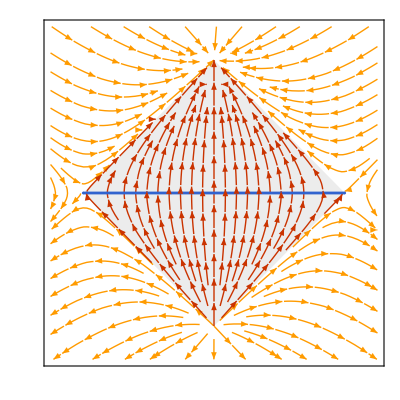

```mathematica
fig1=Show[
StreamPlot[ξbplot[x,t,-1,1,0,-1],{x,-1.25,1.25},{t,-1.25,1.25},
StreamScale-> {.075,Automatic,Automatic},StreamStyle->Directive[RGBColor[1., 0.607843, 0.]],FrameTicks->None,GridLines->None],
Graphics[{Gray,Thickness[0.005],Opacity[.15],Polygon[{{-1,0},{0,1},{1,0},{0,-1}}]}],
StreamPlot[ξbplot[x,t,-1,1],{x,-1.15,1.15},{t,-1.15,1.15},
StreamScale-> {.075,Automatic,Automatic},StreamStyle->Directive[RGBColor[0.790588, 0.201176, 0.]],FrameTicks->None,GridLines->None],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thickness[0.005],Opacity[1],Line[{{-1,0},{1,0}}]}],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thick,Opacity[1],Disk[{-1,0},.01]}],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thick,Opacity[1],Disk[{1,0},.01]}],
ImageSize->400
]
```

```mathematica
Export["~/Library/Mobile\ Documents/com~apple~CloudDocs/iPad/Lflow.png",Show[fig1],"PNG"]
```

~/Library/Mobile Documents/com~apple~CloudDocs/iPad/Lflow.png

Plot in Euclidean signature:

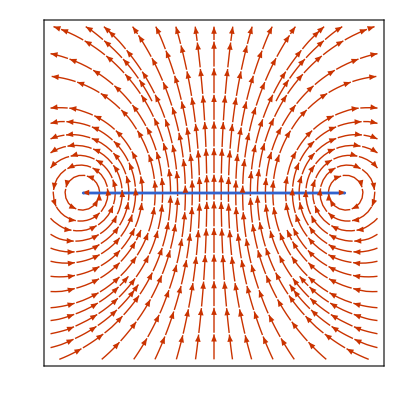

```mathematica
fig2=Show[
StreamPlot[ξbplot[x,t,-1,1,2,1],{x,-1.25,1.25},{t,-1.25,1.25},
StreamScale-> {.075,Automatic,Automatic},StreamStyle->Directive[RGBColor[0.790588, 0.201176, 0.]],FrameTicks->None,GridLines->None],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thickness[0.005],Opacity[1],Line[{{-1,0},{1,0}}]}],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thick,Opacity[1],Disk[{-1,0},.01]}],
Graphics[{RGBColor[0.192157, 0.388235, 0.807843],Thick,Opacity[1],Disk[{1,0},.01]}],
ImageSize->400
]
```

```mathematica
Export["~/Library/Mobile\ Documents/com~apple~CloudDocs/iPad/Eflow.png",Show[fig2],"PNG"]
```

~/Library/Mobile Documents/com~apple~CloudDocs/iPad/Eflow.png

```mathematica
{1/2 ξ.{1,1,0},1/2 ξ.{1,-1,0},ξ⟦-1⟧}/.{u->x+t,v->x-t,SubPlus[u]->1,SubPlus[v]->1,SubMinus[u]->-1,SubMinus[v]->-1}//Simplify
```

{-2 π t x,-π (-1+t^2+x^2+z^2),-2 π t z}

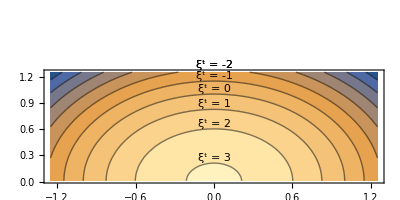

```mathematica
fig3=Show[
ContourPlot[
1/2 ξ.{1,-1,0}/.{u->x,v->x,SubPlus[u]->1,SubPlus[v]->1,SubMinus[u]->-1,SubMinus[v]->-1}//Evaluate,
{x,-1.25,1.25},{z,0.01,1.25},
AspectRatio->Automatic,
ContourLabels->(Text["ξ^t = "<>ToString@#3,{0,√(#1^2+#2^2)},{0,-1},Background->{White,Opacity[.5]}]&)
],
ImageSize->400
]
```

Note that ξ^x,ξ^z both vanish in the t=0 plane. ξ^t=0 corresponds to the RT surface, where ξ^μ vanish entirely.

```mathematica
{1/2 ξ.{1,-1,0},ξ⟦-1⟧}/.{u->x+t,v->x-t,SubPlus[u]->1,SubPlus[v]->1,SubMinus[u]->-1,SubMinus[v]->-1}//Simplify
```

{-π (-1+t^2+x^2+z^2),-2 π t z}

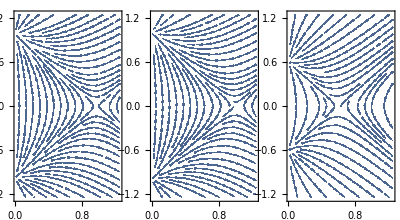

```mathematica
fig4=GraphicsRow[
StreamPlot[
{ξ⟦-1⟧,1/2 ξ.{1,-1,0}}/.{u->x+t,v->x-t,SubPlus[u]->1,SubPlus[v]->1,SubMinus[u]->-1,SubMinus[v]->-1}/.x->#//Simplify//Evaluate,
{z,0.01,1.25},{t,-1.25,1.25},
AspectRatio->Automatic,
StreamScale-> {.075,Automatic,.012},
StreamPoints->200,
StreamMarkers->"Pointer"
]&/@{-.2,0,.8},
ImageSize->400
]
```

#### Modular flow generator at the cutoff surface

Rapidity θ parametrize the boost of the interval:

```mathematica
$Assumptions=L>0;

FullSimplify[ξ/.{SubMinus[u]->-SubPlus[u],SubMinus[v]->-SubPlus[v]}/.{SubPlus[u]->SubPlus[x]+SubPlus[t],SubPlus[v]->SubPlus[x]-SubPlus[t]}]//Together//Collect[#,SubPlus[x]]&//ExpandDenominator

%//.{SubPlus[x]->L/2 Cosh[θ],SubPlus[t]->L/2 Sinh[θ]}//Simplify

((Hold[({{D[t, u], D[t, v], 0}, {D[x, u], D[x, v], 0}, {0, 0, 1}})]/.xt2uv//ReleaseHold).%)/.uv2xt//Simplify

collectCoefficient[%,(2π)/L,FullSimplify]
```

{(π (t_+^3-t_+ u^2+t_+^2 x_++u^2 x_+-t_+ x_+^2-x_+^3+t_+ z^2+x_+ z^2))/(t_+^2-x_+^2),(π (t_+^3-t_+ v^2-t_+^2 x_+-v^2 x_+-t_+ x_+^2+x_+^3+t_+ z^2-x_+ z^2))/(t_+^2-x_+^2),-(π (t_+ u+t_+ v-u x_++v x_+) z)/(t_+^2-x_+^2)}

{(π ((L^2-4 (u^2+z^2)) Cosh[θ]+(L^2+4 u^2-4 z^2) Sinh[θ]))/(2 L),(π ((-L^2+4 (v^2+z^2)) Cosh[θ]+(L^2+4 v^2-4 z^2) Sinh[θ]))/(2 L),-(2 π z ((u-v) Cosh[θ]-(u+v) Sinh[θ]))/L}

{(π ((L^2-4 (t^2+x^2+z^2)) Cosh[θ]+8 t x Sinh[θ]))/(2 L),(π (-8 t x Cosh[θ]+(L^2+4 (t^2+x^2-z^2)) Sinh[θ]))/(2 L),-(4 π z (t Cosh[θ]-x Sinh[θ]))/L}

(2 π)/L {1/4 (L^2-4 (t^2+x^2+z^2)) Cosh[θ]+2 t x Sinh[θ],-2 t x Cosh[θ]+1/4 (L^2+4 (t^2+x^2-z^2)) Sinh[θ],-2 t z Cosh[θ]+2 x z Sinh[θ]}